```mathematica
SetDirectory[NotebookDirectory[]]
posLEDS = Import["location_LEDS.csv","CSV"];
```

C:\Users\caramirezs\My Drive\Python\Luces_Mom

```mathematica
(*parámetros iniciales*)
nLEDS = 750;
frames = 900;
r=1.3*1;h =5;
(*Cono*)
ℛ=Cone[{{0,0,0},{0,0,h}},r];
```

```mathematica
(*creación de puntos aleatorios - coordenadas cilídricas*)
(*altura aleatoria*)
rdmh=RandomReal[{0,h}];
(*ángulo*)
rdmangle= RandomReal[{0, 2Pi}];
(*radio circunferencia*)
rdmx=RandomReal[{0, (r(h-rdmh))/h}];
(*coordenadas de los puntos*)
posLEDS=Table[ (
rdmh=RandomReal[{0,h}];
rdmangle= RandomReal[{0, 2Pi}];
rdmx=RandomReal[{0.7 ((r(h-rdmh))/h), (r(h-rdmh))/h}];
{rdmx Cos[rdmangle],rdmx Sin[rdmangle],rdmh}),{i,1,nLEDS}];
Graphics3D[{AbsolutePointSize@5, Point@posLEDS, Opacity@0.5,ℛ }]
```

-Graphics3D-

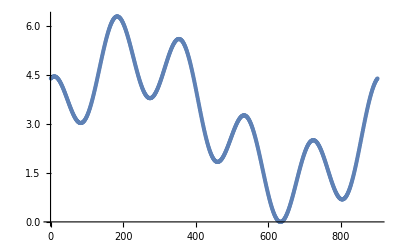

```mathematica
(*Curva por donde se va a mover la esfera*)
(*ángulo*)
fAngulo[f_]:=0.8Sin[(10π 0.2 f)/frames]+0.5Cos[(10π  f)/frames]
listatemp = fAngulo[f]/.f->Range[0,frames,1];
listaangulos = Rescale[listatemp,MinMax[listatemp],{0,2π}];
ListPlot[listaangulos]
```

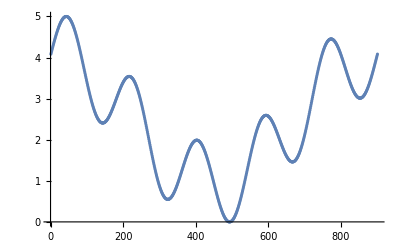

```mathematica
(*altura*)
fAltura[f_]:=0.5Sin[(10π  f)/frames]+0.8Cos[(10π 0.2 f)/frames]
listatemp = fAltura[f]/.f->Range[0,frames,1];
listaaltura = Rescale[listatemp,MinMax[listatemp],{0,h}];
ListPlot[listaaltura]
```

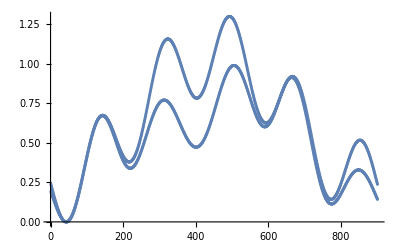

```mathematica
(*radio circunferencia*)
rtemp = (r(h-htemp))/h/.htemp->listaaltura;
ttemp=0.2Sin[(3.5π)/900 f]+0.8/.f->Range[0,frames,1];
listarho = rtemp*ttemp;
Show[
ListPlot[rtemp],
ListPlot[listarho]
]
```

```mathematica
(*curva de movimiento*)
curvaparam = Table[{listarho[[i]] Cos[listaangulos[[i]]],listarho[[i]] Sin[listaangulos[[i]]], listaaltura[[i]]},{i,1,frames}];
Show[Graphics3D[{Opacity@0.2,AbsolutePointSize@4, Point@posLEDS, Opacity@0.2,ℛ }],
ListPointPlot3D[curvaparam]]
```

-Graphics3D-

```mathematica
(*radio esfera que se mueve por la curva*)
raEsfera = 0.4;
(*Manipulación para revisar el movimiento*)
Manipulate[
(*solamente pintar los puntos que están en la esfera*)
valorVerdad = Map[RegionMember[Ball[curvaparam[[a]],0.5],#]&,posLEDS];
posVerdad := Flatten[Position[valorVerdad,True]];
puntosinsphere := posLEDS[[posVerdad]];
Show[
Graphics3D[{AbsolutePointSize@3, Point@puntosinsphere,Opacity@0.2,AbsolutePointSize@3, Point@posLEDS, Opacity@0.2,ℛ  }],
Graphics3D[{Opacity@0.2,Sphere[curvaparam[[a]],raEsfera]}],
ListPointPlot3D[curvaparam]],
{a,1,900,1}]
```

```mathematica
(*posición de los led que se prenden por fram (x900)*)
tablaposCurva = Table[
Flatten[Position[ParallelMap[RegionMember[Ball[curvaparam[[f]],raEsfera],#]&,posLEDS],True]],{f,1,frames,1}
];
(*matriz frames x 250 para saber cuales led se encienden*)
listatemp = ConstantArray[x,{frames,nLEDS}];
For[i=1,i≤frames,i++,
(listatemp[[i]][[tablaposCurva[[i]]]]=y)];
(*vista*)
```

```mathematica
(*colores de los led-x y led-y*)
color1={0,255,0}; color2={255,0,0};
listatemp = listatemp/.{x->color1, y->color2};
(*Ejemplo del primer frame*)
listatemp[[1]];
(*se debe hacer flatten y lugo dividirlo nuevamente por Frames*)
listaFrames = Partition[Flatten[listatemp],nLEDS*3];
```

```mathematica
encabezado =Flatten[ Table[{StringJoin["R_",ToString[i]],StringJoin["G_",ToString[i]],StringJoin["B_",ToString[i]]},{i,0,nLEDS-1}]];
linea0 = Prepend[Range[frames],"FRAME_ID"];
PrependTo[listaFrames,encabezado];
listaFrames = Transpose[Prepend[Transpose[listaFrames],linea0]]
```

{1}
 |  |  |  |

```mathematica
Export["C:\\Users\\caramirezs\\My Drive\\Python\\Luces_Mom\\curva.csv",listaFrames,"CSV", "TextDelimiters" -> ""]
```

```mathematica
"C:\\Users\\caramirezs\\My Drive\\Python\\Luces_Mom\\curva.csv"
```

C:\Users\caramirezs\My Drive\Python\Luces_Mom\curva.csv